{0.0158489,6.30957×10^-7}

0.1+H-OH-b[2]-2 b[3]==0
b[1]+b[2]+b[3]==0.1
H OH==1/100000000000000
0.0158489==(H b[2])/b[1]
6.30957×10^-7==(H b[3])/b[2]

-3.28567×10^24 H+3.28566×10^25 H^2+3.80641×10^32 H^3+3.28567×10^33 H^4==3.28567×10^11

H→0.0000928279

PH→4.03232

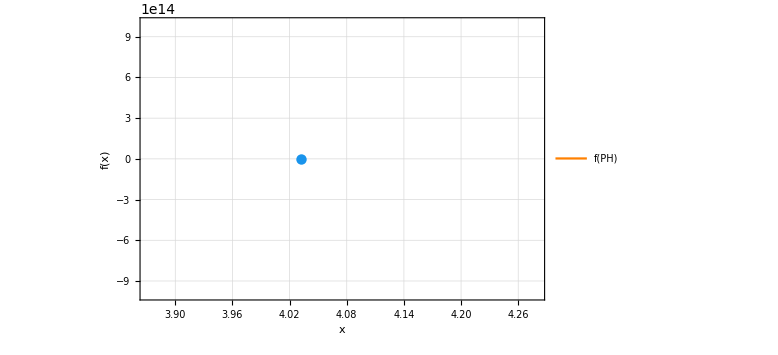

```mathematica
Ka=ChemicalData[Entity["Chemical","PhosphorousAcid"],"AcidityConstants"]                      (*读取离解常数*)

Kw=10^-14;cacid=0.1;cbase=0.1;                                (*cacid是弱酸的分析浓度，cbase是强碱的分析浓度*)

ionizenumber=Length[Ka];                                               (*电离次数，也是电离平衡方程的个数*)
charge=Table[i,{i,0,-ionizenumber,-1}];     (*由于溶质电离而产生的粒子，各自的带电量*)

ionize=Table[b[i],{i,1,Length[charge]}];
(*溶质电离产生的粒子，用b[i]代替，i在此处也标明第几级电离，后面按这个顺序列出所有与平衡常数相关的方程集合：equilibriums*)

solutionall=Join[ionize,{H},{OH}];                   (*溶液中所有的粒子（把H和OH加进ionize），作为最终方程的变量*)

chargedsolution=Join[Table[charge[[n]]*ionize[[n]],{n,1,Length[charge]}],{H},{-OH},{cbase}];
                                                                                                     (*粒子乘以电荷，加上H、OH还有Na，方便列出CBE*)


CBE=Total[chargedsolution];
MBE=Total[ionize];
water=H*OH;
equilibriums=Table[Ka[[n]]==(b[n+1]*H)/b[n],{n,1,Length[Ka]}];
Column[list=Join[{CBE==0,MBE==cacid,water==Kw},equilibriums]]                (*列出所有的方程*)


aim=Eliminate[list,Join[{OH},ionize]]
Solve[Join[{aim},{H>0}],solutionall,Reals][[1,1]]
aimPH=Eliminate[Join[{aim},{PH==-Log10[H]}],{H}];
aimPH=AddSides[aimPH,-aimPH[[2]]];
NSolve[aimPH,PH,Reals][[1,1]]
sol=NSolve[aimPH,PH,Reals][[1,1,2]];                                                                           (*消除变量*)


points1=Table[{i,NSolve[{PH==i,y==aimPH[[1]]},{PH,y},Reals][[1,2,2]]},{i,sol-0.4+0.2472,sol+0.2472,0.0001}];
Show[ListLinePlot[points1,ImageSize->Large,PlotTheme->"Detailed",PlotStyle->RGBColor[1, 0.5, 0],FrameLabel->{{HoldForm[f[x]],None},{HoldForm[x],None}},LabelStyle->{11,GrayLevel[0]},PlotLegends->{"f(PH)"}],Graphics[{RGBColor[0.09778905418725503, 0.58, 0.9269455007318339],PointSize[0.013],Point[{sol,0}]}]]   (*作图*)
```

3.28567×10^33 10.^(-4. PH)+10.^(-3. PH) (3.80641×10^32-(3.28567×10^32)/(1.+R))+10.^(-2. PH) (5.20746×10^30-(1.04149×10^31)/(1.+R))+10.^(-1. PH) (3.28567×10^24-(9.857×10^24)/(1.+R))==3.28567×10^11&&1.+R≠0.

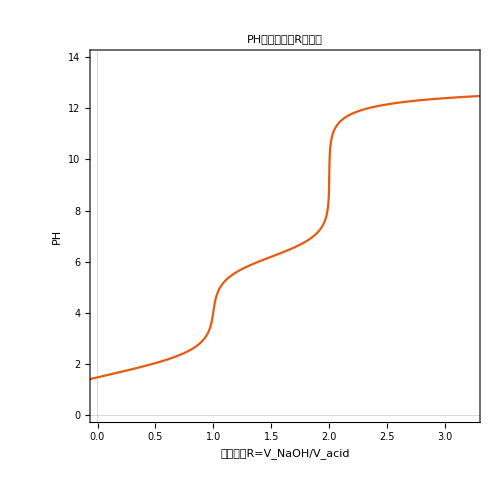

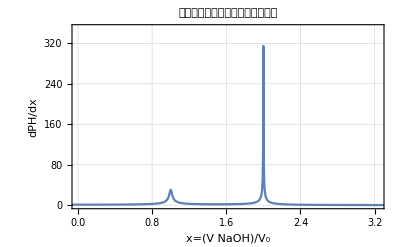

```mathematica
Ka=ChemicalData[Entity["Chemical","PhosphorousAcid"],"AcidityConstants"];

Kw=10^-14;cacid=0.1;cbase=0.1;                             (*cacid弱酸起始浓度，cbase强碱浓度*)

ionizenumber=Length[Ka];
charge=Table[i,{i,0,-ionizenumber,-1}];
ionize=Table[b[i],{i,1,Length[charge]}];
solutionall=Join[ionize,{H},{OH}];
chargedsolution2=Join[Table[charge[[n]]*ionize[[n]],{n,1,Length[charge]}],{H},{-OH},{cb}];
                                                                 (*和前面的，区别之处在于符号性的ca和cb*)

CBE2=Total[chargedsolution2];
MBE=Total[ionize];
water=H*OH;
equilibriums=Table[Ka[[n]]==(b[n+1]*H)/b[n],{n,1,Length[Ka]}];

list2=Join[{CBE2==0,MBE==ca,water==Kw},equilibriums];           (*新的list2，为绘制滴定进程曲线*)
newaim=Eliminate[Join[{cb==(cbase*R)/(1+R),ca==cacid/(1+R),PH==-Log10[H]},list2],Join[solutionall,{cb,ca}]]
(*引入滴定进程R*)


points2=Table[{NSolve[{PH==i,newaim},{R,PH},Reals][[1,2,2]],i},{i,0,14+Log10[cbase],0.005}];
Show[ListLinePlot[points2,PlotTheme->"Scientific",FrameLabel->{{HoldForm[PH],None},{HoldForm[滴定进程R=Subscript[V, NaOH]/Subscript[V, acid]],None}},PlotLabel->HoldForm[PH随滴定进程R变化图],LabelStyle->{16,GrayLevel[0]},PlotRange->{{0,1/0.618*Length[Ka]*cacid/cbase},{0,15+Log10[cbase]}}],ImageSize->{500,500},AspectRatio->Full]
(*作图*)
x=Table[points2[[i,1]],{i,1,Length[points2]}];
dy=0.005;
diffrential=Table[{x[[i]],dy/(x[[i+1]]-x[[i]])},{i,1,Length[points2]-1}];
ListLinePlot[diffrential,PlotTheme->"Detailed",FrameLabel->{{HoldForm[dPH/dx],None},{HoldForm[x=(V(NaOH))/Subscript[V, 0]],None}},PlotRange->{{0,1/0.618*Length[Ka]*cacid/cbase},{0,350}},PlotLabel->HoldForm[滴定曲线的差分随滴定进程变化图],LabelStyle->{16,GrayLevel[0]},ImageSize->Full]
```

```mathematica
list
ionize
NSolve[Join[list,{H>0}],Join[{H,OH},ionize]]
```

{0.1+H-OH-b[2]-2 b[3]==0,b[1]+b[2]+b[3]==0.1,H OH==1/100000000000000,0.065==(H b[2])/b[1],0.000061==(H b[3])/b[2]}

{b[1],b[2],b[3]}

{{b[1]→0.00221521,OH→0,b[3]→0.00374638,b[2]→0.0940384,H→0.00153117}}

```mathematica
ChemicalData[Entity["Chemical","SulfuricAcid"],"AcidityConstants"]
```

{630.,0.0102}

```mathematica
Eliminate[{0.1+H-OH-b[2]-2 b[3]-3b[4]==0,b[1]+b[2]+b[3]+b[4]==0.1,H OH==1/100000000000000,0.0079432823472428134`2.==(H b[2])/b[1],6.3095734448`2.*^-8==(H b[3])/b[2],b[4]/b[3]==2},{OH,b[1],b[2],b[3],b[4]}]
```

False

```mathematica
2
```

2

```mathematica
list
```

{0.1+H-OH-b[2]-2 b[3]-3 b[4]==0,b[1]+b[2]+b[3]+b[4]==0.1,H OH==1/100000000000000,0.0079==(H b[2])/b[1],6.3×10^-8==(H b[3])/b[2],5.01×10^-13==(H b[4])/b[3]}

```mathematica
Column[Join[{cb==(cbase*R)/(1+R),ca==cacid/(1+R),PH==-Log10[H]},list2]]
```

cb==(0.1 R)/(1+R)
ca==0.1/(1+R)
PH==-Log[H]/Log[10]
cb+H-OH-b[2]-2 b[3]==0
b[1]+b[2]+b[3]==ca
H OH==1/100000000000000
0.065==(H b[2])/b[1]
0.000061==(H b[3])/b[2]

```mathematica
NSolve[{PH==5,newaim},{PH,R}]
```

{{PH→5.,R→1.85883}}

```mathematica
list
Eliminate[{0.1+H-OH-b[2]-2 b[3]-3 b[4]==0,b[1]+b[2]+b[3]+b[4]==0.1,H OH==1/100000000000000,0.0079432823472428134`2.==(H b[2])/b[1],6.3095734448`2.*^-8==(H b[3])/b[2],b[4]==H/b[3]},Join[{OH},ionize]]
```

{0.1+H-OH-b[2]-2 b[3]-3 b[4]==0,b[1]+b[2]+b[3]+b[4]==0.1,H OH==1/100000000000000,0.0079==(H b[2])/b[1],6.3×10^-8==(H b[3])/b[2],5.01×10^-13==(H b[4])/b[3]}

False

```mathematica
ChemicalData[]
```

{liquid hydrogen,hydrogen,deuterium hydride,liquid helium,helium,tritium hydride,deuterium,tritium deuteride,hydrogen-t2,lithium,lithium hydride,lithium deuteride,beryllium,boron,beryllium hydride,diamond,activated charcoal,graphite,carbon-13,borane,liquid methane,methane,ammonia,methane-13 C,methane-d 1,steam,ice,water,ammonia-15 N,methane-d 2,methane-d 3,deuterium fluoride,hydrofluoric acid,hydrogen fluoride,water-18 O,heavy water,ammonia-d 3,methane-d 4,liquid neon,neon,ammonia-15 N,d 3,methane-13 C,d 4,lithium borohydride,methyllithium,water-t2,lithium amide,sodium,lithium hydroxide,sodium hydride,magnesium,boron nitride,lithium deuteroxide,beryllium oxide,lithium fluoride,acetylene,magnesium hydride,aluminum,hydrogen cyanide,diborane,borane-ammonia complex,carbon monoxide,carbon-13C monoxide,liquid nitrogen,nitrogen,acetylene-d 2,ethylene,silicon,dry air,liquid air,lithium oxide,nitrogen-15 N2,nitric oxide,formaldehyde,paraform,diazine,beryllium carbide,ethylene-13 C2,ethane,beryllium boride,black phosphorus,red phosphorus,nitric-15 noxide,formaldehyde-13 c,methylamine,ethane-13 C1,ethane-d 1,sulfur 32,liquid oxygen,oxygen,paraformaldehyde-d 2,formaldehyde-d 2,methanol,diazane,ethane-13 C2,mixed sulfur,ethylene-d 4,terminal dimethyl,silane,nitric-15 noxide-18 O,hydroxylamine,methanol-13 C,methanol-d,methan-d 1-ol,diborane-d 610%in D2,electronic grade,lithium-aluminum alloy,sulfur 34,phosphine,hydrogen peroxide,fluoromethane,methanol-18 O,methan-d 2-ol,hydrogen sulfide,methyl-d 3-amine,ethane-1,1,2,2-d 4,fluoramine,fluoromethane-13 C,ammonium hydroxide,deuterated methanol (D3),ethane-d 5,oxygen-18 O2,ethyllithium,ammonium-15 nhydroxide,deuterated methanol (D4),hydrazine-d 4dideuteriochloride,deuterium sulfide,methylamine-d 5,ethane-d 6,43836,n-benzoyl-D-arginine-1-4-nitroaniline,N-acetyl-β-D-glucosaminyl-1,6-(N-acetyl-β-D-glucosaminyl-1,3)-N-acetyl-D-galactosaminyl-R,n-acetyl-1,3-beta-D-galactosaminylproteoglycan,retinyl-ester-(cellular-retinol-binding-protein),6-(alpha-D-glucosaminyl)-1d-myo-inositol,o-acylcarnitine,rhizobactin 1021 core,n-acyl-L-glutamine,heparosan-n-sulfate d-glucuronate,acyldolichol,7,2'-dihydroxy-4'-methoxy-isoflavanol-quinonemethide-intermediate-2,7,2'-dihydroxy-4'-methoxy-isoflavanol-quinonemethide-intermediate-1,beta-hydroxypyrivate,diacylglycerol pyrophosphate,diacylglycerol phosphate,n-acetyl-alpha-D-glucosaminyl-(1->4)-beta-D-glucuronosyl-(1->4)-n-acetyl-alpha-D-glucosaminylproteoglycan,beta-D-glucuronosyl-(1->4)-n-acetyl-alpha-D-glucosaminyl-(1->4)-beta-D-glucuronosylproteoglycan,beta-D-galactosyl-1,4-n-acetyl-beta-D-glucosaminylglycopeptide,n-acetyl-beta-D-glucosaminyl-glycopeptide,beta-D-glucuronosyl-(1->4)-n-acetyl-alpha-D-glucosaminylproteoglycan,4,5-dioxo-3α,4,5,6,7,8,9,9β-octahydro-1h pyrrolo[2,3-f]quinoline-2,7,9-tricarboxylate,1,4-beta-D-galactosyl-(alpha-1,3-L-fucosyl)-n-acetyl-D-glucosaminyl-r,1,4-beta-D-galactosyl-n-acetyl-D-glucosaminyl-r,beta-D-glucuronosyl-(1->3)-n-acetyl-beta-D-galactosaminyl-(1->4)-beta-D-glucuronosylproteoglycan,ndp-aldose,n-palmitoylglycoprotein,calmodulin n6-methyl-L-lysine,glycoprotein,oligosaccharide containing 6-methyl-D-glucose units,o-palmitoylglycoprotein,mucus glycoprotein,oligoglycosylglucose,o-beta-D-xylosylprotein,[3-methylcrotonoyl-CoA:carbon-dioxide ligase(adp-forming)],colanic acid,mlps,propionyl-amp,alpha-n-acetyl-D-glucosaminyl-(1->4)-beta-D-glucuronosyl-(1->3)-beta-D-galactosyl-(1->3)-beta-D-galactosyl-(1->4)-beta-D-xylosylproteoglycan,oligoglycosylglucosylceramide,[acetyl-CoA carboxylase],a 4-hydroxyacid,histone-L-lysine,apo-[3-methylcrotonoyl-CoA:carbon-dioxide ligase (adp-forming)],[acetyl-CoA carboxylase] phosphate,1,4-alpha-D-glucooligosaccharide,heparosan-n-sulfate l-iduronate,n-acetyl-beta-D-galactosaminyl-(1->4)-beta-D-glucuronosylproteoglycan,cutin monomer,n-acetyl-alpha-D-glucosaminyl-(1->4)-beta-D-glucuronosylproteoglycan,D-mannosylglycoprotein,excised base,n-acetyl-D-galactosaminoglycan,external aldimine,6-(d-glucose-1-phospho)-D-mannosylglycoprotein,alpha-D-aldose 1-phosphate,protein beta-D-galactosyl-L-hydroxylysine,caldesmon phosphate,caldesmon,myosin light-chain,myosin light-chain phosphate,cutin,D-galactosaminoglycan,calmodulin l-lysine,L-ala-D-glu-2pm,a phospholipid methylene fatty acid,c20 skeleton,methyl-beta-D-glucuronide,c19 skeleton,17a-hydroxy-progesterone,D-(-)-3-hydroxybutyrate,2-monoacylglycerol,1-monoacylglycerol,allo-4-hydroxy-D-proline,L-cysteine sulfinate,3-ketothreonine,an alpha amino acid ester,[formate c acetyltransferase]-glycine,[formate c acetyltransferase]-glycin -2-yl radical,protein c-terminal s-farnesyl-L-cysteine,protein c-terminal s-farnesyl-L-cysteine methyl ester,protein n6-methyl-L-lysine,protein-n-ubiquityl-lysine,protein tyrosine-o-sulfate,protein-n-acetyl-D-glucosaminyl)hydroxyproline,antidiuretic hormone,heparan sulfate,chromomycin a3,dextran,fumonisin b2,growth hormone-releasing hormone,hyaluronate,low density lipoprotein,signal recognition particle,trichostatin a,α-amanatin,ammonium metatungstate hexahydrate,cerium(III) acetate sesqihydrate,xenon fluoride undecafluoroantimonate,bacteriochlorophyll b,5-hydroxybenzimidazolylcobamide,co-5-hydroxybenzimidazolylcob(I)amide,ferric enterobactin,quinine sulfate dihydrate,methyl cellulose,sodium hexachloroiridate(IV) hexahydrate,brij58,brij78,triton®X-100 reduced,dihydrogen hexahydroxyplatinate(IV),carbonyldihydridotris(triphenylphosphine)ruthenium(II),dihydridotetrakis(triphenylphosphine)ruthenium(II),4-(2,3-dihydroxypropyl)-2-(2-methylene-4,4-dimethylpentyl)succinate potassium salt,triarylsulfonium hexafluoroantimonate salts,acetic acid,alkyl(C9 to C11)esters mixture,glycolic acid ethoxylate oleyl ether,cytosine-2,4-13 C2,15 N3,PSS-isooctyl substituted.cage mixture,n=8,10,12,3-acetylpyridine-nad,bacteriochlorophyll c,tetraearbonyldihydroiron,fe-mo cofactor,1,2-dehydroreticuline,sulfoquinovosyldiacylglycerol,iron phosphide (1:1),cobyrate,ag4}
 |  |  |  |

```mathematica
ChemicalData[EntityClass["Chemical","Acids"],"AcidityConstants"]
```

$Aborted